```mathematica
SetDirectory["/Users/dd/pCloud Drive/data/population/data/"]
```

/Users/dd/pCloud Drive/data/population/data

```mathematica
allfile = FileNameJoin[{Directory[], "global", "all_global.csv"}]
```

/Users/dd/pCloud Drive/data/population/data/global/all_global.csv

```mathematica
alldata = Import[allfile, "Dataset", "HeaderLines"->1]
```

```mathematica
alldata2024 = alldata[Select[#year >= 2024 &]]
```

```mathematica
alldata2024[All, "year"]
```

```mathematica
v = alldata2024[All, "un2024_Low"] // Normal;
 t = alldata2024[All, "year"] // Normal
```

{2024,2025,2026,2027,2028,2029,2030,2031,2032,2033,2034,2035,2036,2037,2038,2039,2040,2041,2042,2043,2044,2045,2046,2047,2048,2049,2050,2051,2052,2053,2054,2055,2056,2057,2058,2059,2060,2061,2062,2063,2064,2065,2066,2067,2068,2069,2070,2071,2072,2073,2074,2075,2076,2077,2078,2079,2080,2081,2082,2083,2084,2085,2086,2087,2088,2089,2090,2091,2092,2093,2094,2095,2096,2097,2098,2099,2100}

```mathematica
es = EventSeries[v, {t}]
```

EventSeries[…]

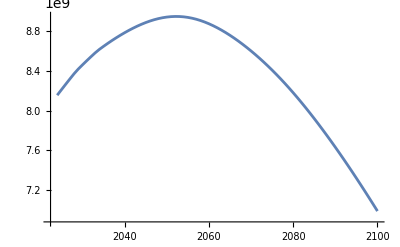

```mathematica
ListLinePlot[es]
```

```mathematica
max = alldata[MinMax, All]
```

```mathematica
Keys[alldata]
```

```mathematica
Information[max]
```